# ray tracing example: Schwarzschild metric

This notebook will guide the user through the main features of the SimpleRayTracer package for Mathematica by use of the example of the Schwarzschild metric. 

In principle, the full notebook can be generalized to arbitrary smooth (black-hole) spacetimes as long they are the metric is known in Boyer-Lindqvist (currently, only these are provided) coordinates. In the current version, also the Christoffel symbols have to be determined previously and have to be provided by the user (xAct integration may be provided in the future).

The metric defines a spacetime in which the SimpleRayTracer package numerically determines lightlike geodesics.

## initialization

... load the package ...

```mathematica
<<SimpleRayTracer`;
```

========================================================================
SimpleRayTracer package is being loaded. =============================
=======================================================================

Set the Boyer-Lindquist coordinates (currently the automatic definition of the camera setup is not possible in other coordinates).

```mathematica
SetBoyerLindquistCoords[t,r,θ,ϕ];
GetBoyerLindquistCoords[]
```

{t,r,θ,ϕ}

Specify metric and connection (Christoffel symbols). Inverse metric is determined by the package itself.

```mathematica
h[r_]:=1-(2*M)/r;
SetMetric[gMetric, {
	{-h[r],0,0,0},
	{0,1/h[r],0,0},
	{0,0,r^2,0},
	{0,0,0,r^2 Sin[θ]^2}
}]
```

```mathematica
SetChristoffel[christoffelOf[gMetric],
{
	{
		{0, D[h[r],r]/(2 h[r]), 0, 0},
		{D[h[r],r]/(2 h[r]), 0, 0, 0},
		{0, 0, 0, 0},
		{0, 0, 0, 0}
	},
	{
		{1/2 h[r] D[h[r],r], 0, 0, 0},
		{0, -D[h[r],r]/(2 h[r]), 0, 0},
		{0, 0, -h[r] r, 0},
		{0, 0, 0, -h[r] r Sin[θ]^2}
	},
	{
		{0, 0, 0, 0},
		{0, 0, 1/r, 0},
		{0, 1/r, 0, 0},
		{0, 0, 0, -Cos[θ] Sin[θ]}
	},
	{
		{0, 0, 0, 0},
		{0, 0, 0, 1/r},
		{0, 0, 0, Cot[θ]},
		{0, 1/r, Cot[θ], 0}
	}
}];
```

After metric and/or Christoffels have been set, these can be output to check successful initialization.

```mathematica
GetMetric[1,1]//Simplify
```

r/(2 M-r)

```mathematica
GetChristoffel[2,-1,-1]//Simplify
```

(M (-2 M+r))/r^3

## single ray traces

The Schwarzschild metric which was initialized before has a single free parameter: the mass M.  In general, all such parameter values have to be passed as rules to all the numerical functions.

GetSingleLightRay[rCam_,θCam_,ϕCam_},{xScreen_,yScreen_},paramRules_List] 
is a function to numerically integrate the geodesic equation of a single light ray in the presently set spacetime. It returns a trajectory as replacement rules for coordinates and momenta.

PlotSingleTrajectory[sol_, paramRules_List]
is a plot routine to plot the trajectory, i.e., the return value of GetSingleLightRay[]. It takes the same options as Mathematica’s Plot3D routine. In addition the user can specify to plot the horizon or not. Note that the numerical routine to determine the horizon surface is costly. If the horizon is known analytically, the user can also pass a region as value for PlotHorizon.

```mathematica
?GetSingleLightRay
?PlotSingleTrajectory
```

You can explore single light rays by varying the screen coordinates below

```mathematica
screenX = 3;
screenY = 2;

sol = GetSingleLightRay[{100,0,0},{screenX,screenY},{M->1}, WorkingPrecision->60][[1]];
Quiet@PlotSingleTrajectory[sol, {M->1}, PlotHorizon->True]
```

trajectory fell into horizon: at λ=100.01 the rr-metric component has surpassed 10^6

plot range obtained by doubling the radial distance at which angular coordinate θ changes most rapidly: use PlotRange option to set own plot range.

{-4.00282842712474619009760337744841939615713935355683811994,4.00282842712474619009760337744841939615713935355683811994}

{θ→1.5708,ϕ→3.14159,r→0.01}

-Graphics3D-

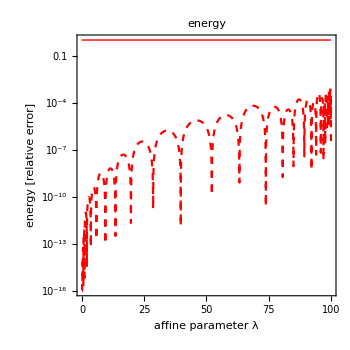

angular momentum seems to vanish identically

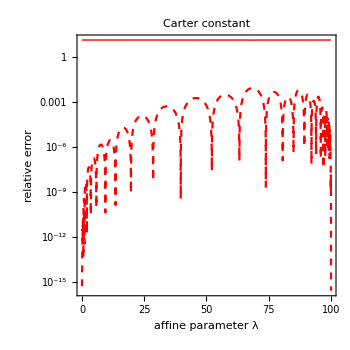

maximalErrors | 0.000743856 | 0. | 0.00810847
finalTimeErrors | 2.717894994173958730246897×10^-29 | 0 | 3.1825394956706483074021979257×10^-28

```mathematica
CheckConstantsOfMotionAlongRay[sol,{M->1}, 0]//TableForm
```

Here is an example for a light ray which marginally falls into the horizon.

```mathematica
sol = GetSingleLightRay[{100,0,0},{36735/10000,36745/10000},{M->1}][[1]];
Quiet@PlotSingleTrajectory[sol, {M->1}, PlotHorizon->True]
```

trajectory fell into horizon: at λ=116.75 the rr-metric component has surpassed 10^6

plot range obtained by doubling the radial distance at which angular coordinate θ changes most rapidly: use PlotRange option to set own plot range.

{-4.0028284271247462,4.0028284271247462}

{θ→1.5708,ϕ→3.14159,r→0.01}

-Graphics3D-

Here is an example for a trajectory which circles the black hole and is just far enough outside to escape again.

```mathematica
MVal = 1;
sol = GetSingleLightRay[{100,0,0},{36745/10000,36745/10000},{M->MVal}][[1]];
Quiet@PlotSingleTrajectory[sol, {M->MVal}, PlotHorizon->True]
```

trajectory escapes: at λ=226.21 the radial coordinate has surpassed the radial camera distance

plot range obtained by doubling the radial distance at which angular coordinate θ changes most rapidly: use PlotRange option to set own plot range.

{-6.04674,6.04674}

{θ→1.5708,ϕ→3.14159,r→0.01}

-Graphics3D-

## shadow boundary

BoundaryBisection[{rCam_,θCam_,ϕCam_}, {{xInnerScreen_,yInnerScreen_}, {xOuterScreen_,yOuterScreen_}}, paramRules_, precisionAim_]
is a routine to perform bisections in a user-defined interval to determine the location of the shadow boundary (if present) within this interval.

```mathematica
?BoundaryBisection
```

You can obtain a single bisection between two screen points to see whether there is a shadow boundary between those points.

```mathematica
x1 = 0; y1 = 0;
x2 = 2; y2 = 2;

Quiet@BoundaryBisection[{100,0,0},{{x1,y1},{x2,y2}},{M->1},1/1000]
```

probably no shadow boundary between the two specified points.

None

Once you have a good idea where the shadow is roughly located, you can obtain a parametric curve of the shadow boundary.
Note that you only have to obtain the upper or lower half of the boundary because all spacetimes which can be written in Boyer-Lindqvist coordinates are symmetric by reflection about the equatorial plane and so are their shadow boundaries.

```mathematica
?GetParametricShadowBoundary
```

```mathematica
sol = Quiet@GetParametricShadowBoundary[{100,0,0}, {0,0}, 8, {1/1000,π,π/10}, {M->1}, 1/1000];
```

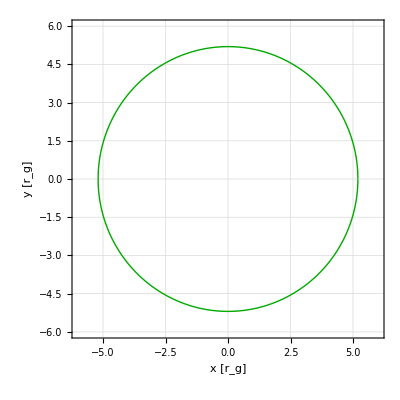

```mathematica
ListPlot[
	Join[sol[[All,2]], Reverse[{#[[1]],-#[[2]]}&/@sol[[All,2]]]],
	PlotRange->{{-6,6},{-6,6}},Joined->True, Axes->False, 
	GridLines->Automatic, GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Gray],
	PlotStyle->{{Darker@Green, Thick}},
	Frame->True, FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},
	FrameLabel->{"x [r_g]", "y [r_g]"}, LabelStyle->{Black,16,FontFamily->"Helvetica"},
	ImageSize->400, AspectRatio->1
]
```